```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yuichirotada/Documents/Univ/general-tail/math

```mathematica
zetaGx[x_,mu_]=mu Sinc[x]//Simplify
```

mu Sinc[x]

```mathematica
zetabar[x_,mu_,γ_]=-1/γ Log[1-γ zetaGx[x,mu]]//Simplify
```

-Log[1-mu γ Sinc[x]]/γ

```mathematica
CompactC[x_,mu_,γ_]=2/3(1-(1+x D[zetabar[x,mu,γ], x])^2)//FullSimplify
```

2/3 (1-(1+(mu (x Cos[x]-Sin[x]))/(x-mu γ Sin[x]))^2)

```mathematica
Cp[x_,mu_,γ_]=D[CompactC[x,mu,γ], x]//Simplify;
```

```mathematica
dRdr[x_,mu_,γ_]=1+x D[zetabar[x,mu,γ], x]//Simplify
```

1+(mu (x Cos[x]-Sin[x]))/(x-mu x γ Sinc[x])

```mathematica
rmcond[x_,mu_,γ_]=-(5 x^20)/mu(D[zetabar[x,mu,γ], x]+x D[D[zetabar[x,mu,γ], x], x])//Simplify
```

-1/(-1+mu γ Sinc[x])^2 5 x^17 (mu x^2 γ Cos[x]^2+Sin[x] (x-x^3+mu γ Sin[x])-x Cos[x] (x+2 mu γ Sin[x])+mu x γ (x Cos[x]+(-1+x^2) Sin[x]) Sinc[x])

```mathematica
rmcond2[x_,mu_,γ_]=1/x(1+x D[zetabar[x,mu,γ], x])//Simplify
```

(-x-mu x Cos[x]+mu Sin[x]+mu x γ Sinc[x])/(x^2 (-1+mu γ Sinc[x]))

```mathematica
Normal[Series[rmcond2[x,1/(2-δ),2-δ],{δ,0,1},{x,0,1}]]
```

x/20+(-1/(2 x)+x/40) δ

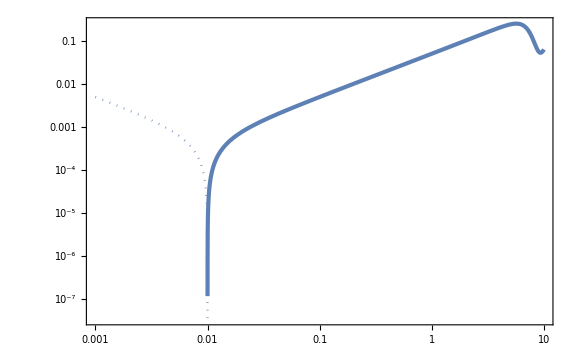

```mathematica
LogLogPlot[{rmcond2[x,1/(2-10^-5)-10^-30,2-10^-5],-rmcond2[x,1/(2-10^-5)-10^-30,2-10^-5]},{x,10^-3,10},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted}},WorkingPrecision->30]
```

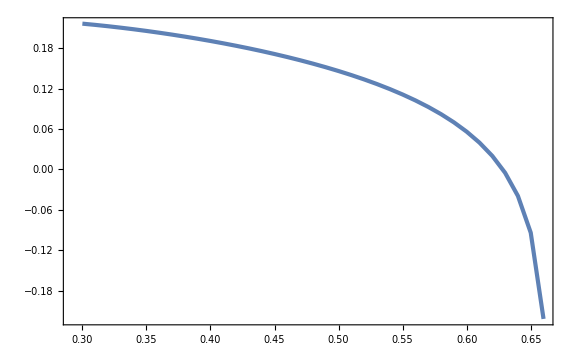

```mathematica
ListPlot[Table[{mu,FindMinimum[{rmcond2[x,mu,3/2],0<x<5},x,WorkingPrecision->30][[1]]//Quiet},{mu,3/10,1/(3/2)-10^-3,10^-2}]]
```

```mathematica
rmcond2minList=Flatten[ParallelTable[{γ,mu,FindMinimum[{rmcond2[x,mu,γ],0<x<5},x,WorkingPrecision->30][[1]]//Quiet},{γ,-6,3/2,10^-2},{mu,3/10,If[γ>0,Min[11/10,1/γ-10^-3],11/10],10^-2}],1];//AbsoluteTiming
```

{213.257,Null}

```mathematica
Export["rmcond2min.dat",rmcond2minList//N];
```

```mathematica
rmcond2minList=Import["rmcond2min.dat"];
```

```mathematica
ListContourPlot[rmcond2minList]
```

-Graphics-

```mathematica
rmcond2minint[γ_,mu_]=Interpolation[rmcond2minList][γ,mu];
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

```mathematica
mu2List=Table[{γ,mu/.FindRoot[rmcond2minint[γ,mu]==0,{mu,3/5},WorkingPrecision->30]//Quiet},{γ,-6,3/2,10^-2}];//AbsoluteTiming
```

{81.6376,Null}

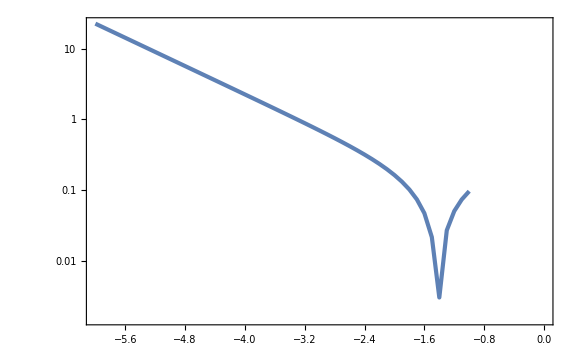

```mathematica
ListLogPlot[Table[{lndmu,Abs[FindMinimum[{rmcond2[x,1/(2-10^(-3/10))-10^lndmu,2-10^(-3/10)],0<x<5},x,WorkingPrecision->30][[1]]//Quiet]},{lndmu,-6,-1,10^-1}]]
```

```mathematica
rmcond2minListfine=Flatten[ParallelTable[{2-10^lndγ,1/(2-10^lndγ)-10^lndmu,FindMinimum[{rmcond2[x,1/(2-10^lndγ)-10^lndmu,2-10^lndγ],0<x<5},x,WorkingPrecision->30][[1]]//Quiet},{lndγ,-3,-3/10,10^-2},{lndmu,-6,-1,10^-2}],1];//AbsoluteTiming
```

{242.034,Null}

```mathematica
Export["rmcond2minfine.dat",rmcond2minListfine//N];
```

```mathematica
rmcond2minListfine=Import["rmcond2minfine.dat"];
```

```mathematica
ListContourPlot[rmcond2minListfine]
```

$Aborted

```mathematica
rmcond2minintfine[γ_,mu_]=Interpolation[rmcond2minListfine][γ,mu];
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

```mathematica
mu2Listfine=Table[{2-10^lndγ,mu/.FindRoot[rmcond2minintfine[2-10^lndγ,mu]==0,{mu,1/3},WorkingPrecision->30]//Quiet},{lndγ,-3,-3/10,10^-2}];//AbsoluteTiming
```

{75.4742,Null}

```mathematica
Export["mu2List.dat",Join[mu2List,Sort[mu2Listfine//N]]//N];
```

```mathematica
mu2Listtot=Import["mu2List.dat"];
```

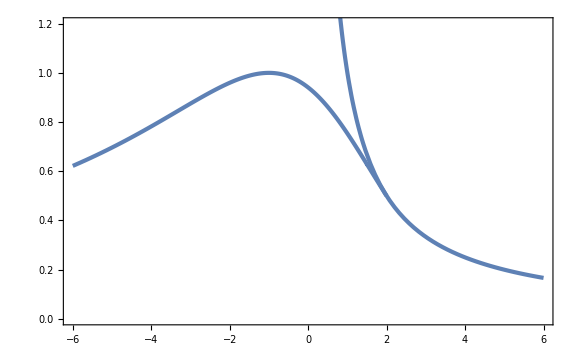

```mathematica
Show[ListPlot[mu2Listtot,PlotRange->{{-6,6},{0,1.2}}],Plot[1/x,{x,0,6}]]
```

```mathematica
mu2int[γ_]=Interpolation[mu2Listtot][γ];
```

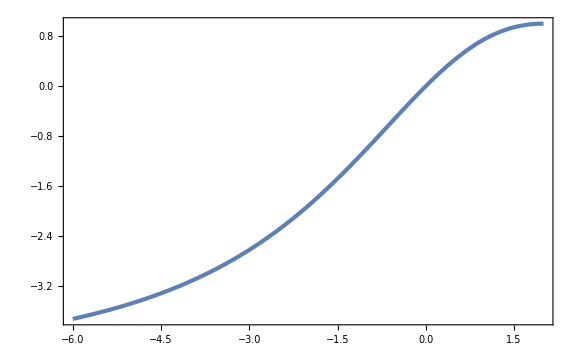

```mathematica
Plot[mu2int[γ]γ,{γ,-6,2}]
```

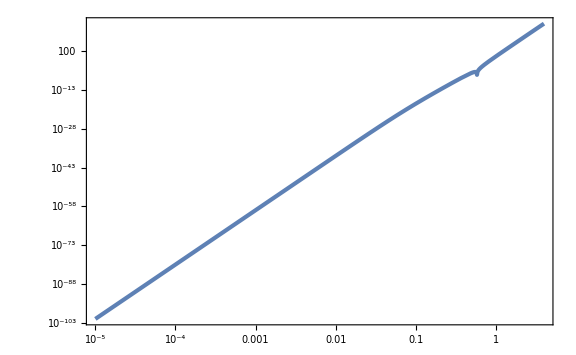

```mathematica
LogLogPlot[Abs[rmcond[x,1,1-10^-3]],{x,10^-5,4},WorkingPrecision->30]
```

```mathematica
xmList=Table[{muγ,x/.FindRoot[rmcond[x,1,muγ]==0,{x,4},WorkingPrecision->30]//Quiet},{muγ,-4,1-10^-3,10^-2}];
```

```mathematica
xm2List=Flatten[ParallelTable[{γ,mu,x/.FindRoot[rmcond2[x,mu,γ]==0,{x,1},WorkingPrecision->30]//Quiet},{γ,-6,2-10^-3,10^-2},{mu,mu2int[γ],1.1,10^-2}],1];//AbsoluteTiming
```

{7.9706,Null}

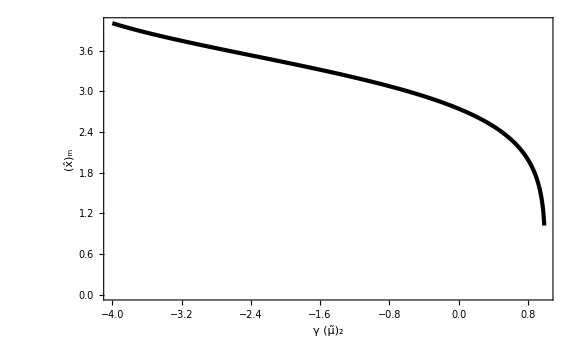

```mathematica
ListPlot[xmList,FrameLabel->{Subscript[OverTilde[μ], 2] γ,Subscript[OverHat[x], "m"]},PlotStyle->{AbsoluteThickness[3],Black}]
```

```mathematica
xmint[muγ_]=Interpolation[xmList][muγ];
xm2int[γ_,mu_]=Interpolation[xm2List][γ,mu];
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

```mathematica
Rarea[x_,mu_,γ_]=E^zetabar[x,mu,γ] x;
```

```mathematica
VMS[mu_,γ_]:=(4π)/3 Rarea[xmint[mu γ],mu,γ]^3/;mu<mu2int[γ];
VMS[mu_,γ_]:=(4π)/3 Rarea[xm2int[γ,mu],mu,γ]^3/;mu>=mu2int[γ];
```

```mathematica
Cbarm[mu_,γ_]:=1/VMS[mu,γ] 4π NIntegrate[CompactC[x,mu,γ] Rarea[x,mu,γ]^2 D[Rarea[x,mu,γ], x],{x,0,xmint[mu γ]}]/;mu<mu2int[γ]
Cbarm[mu_,γ_]:=1/VMS[mu,γ] 4π NIntegrate[CompactC[x,mu,γ] Rarea[x,mu,γ]^2 D[Rarea[x,mu,γ], x],{x,0,xm2int[γ,mu]}]/;mu>=mu2int[γ]
```

```mathematica
CbarmList=Flatten[ParallelTable[If[γ==0,Nothing,{γ,mu,Cbarm[mu,γ]//Quiet}],{γ,-2,6,10^-2},{mu,10^-2,If[γ>0,Min[1.1,1/γ-10^-2],1.1],10^-2}],1];//AbsoluteTiming
```

{191.195,Null}

```mathematica
Export["Cbarm.dat",CbarmList];
```

```mathematica
CbarmList=Import["Cbarm.dat"]//ToExpression;
```

```mathematica
Cbarmint[γ_,mu_]=Interpolation[CbarmList][γ,mu];
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

Interpolation::umprec: Interpolation on unstructured grids is currently only supported for machine numbers. The data will be coerced to machine precision.

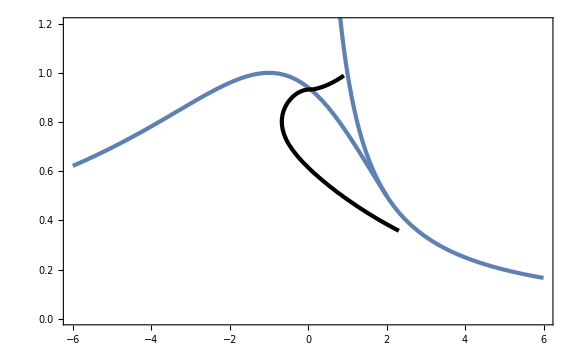

```mathematica
Show[Plot[mu2int[γ],{γ,-6,2},PlotRange->{{-6,6},{0,1.2}}],Plot[1/γ,{γ,0,6}],ContourPlot[Cbarmint[γ,mu]UnitStep[1-mu γ],{γ,-6,6},{mu,10^-2,1.1},Contours->{2/5},ContourShading->None,ContourStyle->{AbsoluteThickness[3]},MaxRecursion->3]]
```

```mathematica
mu2int[1.2]
```

0.704597

```mathematica
Cbarm[0.9,1.2]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.678881}. NIntegrate obtained 7.48301×10^17+2.77664×10^15 ⅈ and 7.37432×10^17 for the integral and error estimates.

7.30011×10^16+2.70878×10^14 ⅈ

```mathematica
xm2int[1.2,0.9]
```

2.97103

InterpolatingFunction::dmval: Input value {1.08} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

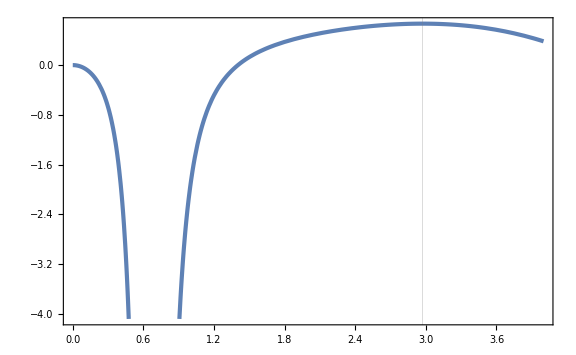

```mathematica
Plot[CompactC[x,0.9,1.2],{x,0,4},GridLines->{{xmint[0.9 1.2],xm2int[1.2,0.9]},None}]
```

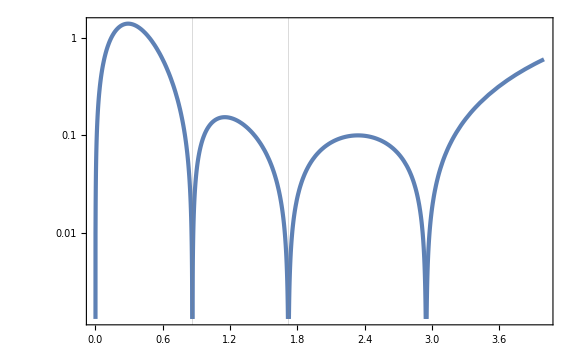

```mathematica
LogPlot[Abs[Cp[x,0.9,1]],{x,0,4},GridLines->{{xmint[0.9],xm2int[1,0.9]},None}]
```

```mathematica
CbarmmaxList=Table[{fNL,FindMaximum[{Cbarmint[fNL,mu],0<mu<1},{mu,0.4}][[1]]},{fNL,-1,0,10^-2}];
```

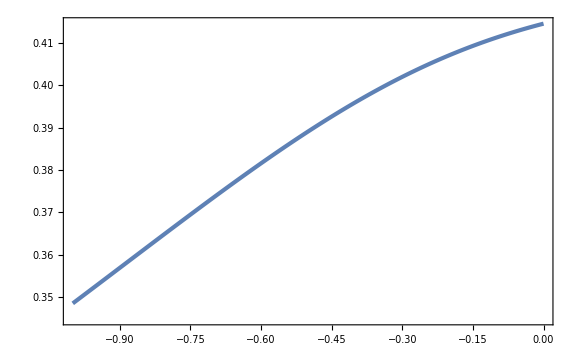

```mathematica
ListPlot[CbarmmaxList,GridLines->{None,{2/5}}]
```

```mathematica
Cbarmmaxint[fNL_]=Interpolation[CbarmmaxList][fNL];
```

```mathematica
fNLmin=fNL/.FindRoot[Cbarmmaxint[fNL]==2/5,{fNL,-0.4}]
```

-0.335546

```mathematica
muthList=Table[{fNL,mu/.FindRoot[Cbarmint[fNL,mu]==2/5,{mu,0.4}]},{fNL,fNLmin,4.1,10^-2}];
```

```mathematica
Plotmuthint[fNL_]=10UnitStep[fNLmin-fNL]+Interpolation[muthList][fNL]UnitStep[fNL-fNLmin];
```

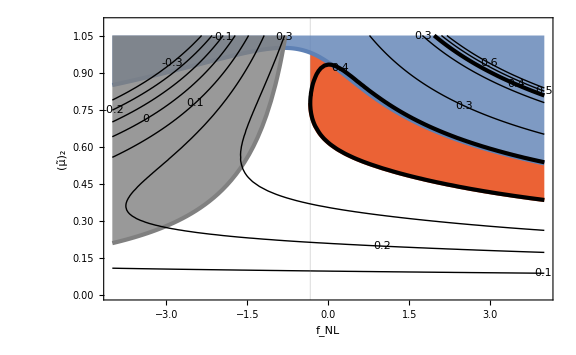

```mathematica
Show[Plot[{mu2int[fNL],Plotmuthint[fNL]},{fNL,fNLmin,4},Filling->{2->{1}},PlotStyle->{None,{AbsoluteThickness[3],Color[4]}},FillingStyle->Opacity[1],AxesOrigin->{-5,-5},PlotRange->{0,1.05},GridLines->{{fNLmin},None}],Plot[mu2int[fNL],{fNL,-4,4},Filling->Top,FillingStyle->Opacity[0.8],PlotRange->{0,1.05}],Plot[-5/(6fNL),{fNL,-4,0},PlotRange->{0,1.05},Filling->Top,PlotStyle->{AbsoluteThickness[3],Gray},FillingStyle->Opacity[0.8],PlotRange->{0,1.05}],ContourPlot[Cbarmint[fNL,mu],{fNL,-4,4},{mu,10^-2,1.05},MaxRecursion->3,Contours->{-0.3,-0.2,-0.1,0,0.1,0.2,0.3,0.4,0.5,0.6},ContourStyle->{Automatic,Automatic,Automatic,Automatic,Automatic,Automatic,Automatic,AbsoluteThickness[3],Automatic,Automatic},ContourShading->None,ContourLabels->(Text[Style[#3,FontFamily->"Palatino",Larger,Background->White],{#1,#2}]&)],PlotRange->{{-4,4},{0,1.1}},FrameLabel->{Subscript[f, NL],Subscript[OverTilde[μ], 2]}]
```

```mathematica
muthint[fNL_]=Interpolation[muthList][fNL];
```

```mathematica
Rareap[x_,mu_,fNL_]=D[Rarea[x,mu,fNL], x]//Simplify;
```

```mathematica
Clear[Cbar2integrand,VMS2integrand,VMS2,Cbar2]
```

```mathematica
cutrate=0;
```

```mathematica
Cbar2integrand[x_,mu_,fNL_]:=CompactC[x,mu,fNL] Rarea[x,mu,fNL]^2 Rareap[x,mu,fNL]/;CompactC[x,mu,fNL]>cutrate CompactC[xmint[mu fNL],mu,fNL]
Cbar2integrand[x_,mu_,fNL_]:=0/;!(CompactC[x,mu,fNL]>cutrate CompactC[xmint[mu fNL],mu,fNL])
```

```mathematica
VMS2integrand[x_,mu_,fNL_]:=Rarea[x,mu,fNL]^2 Rareap[x,mu,fNL]/;CompactC[x,mu,fNL]>cutrate CompactC[xmint[mu fNL],mu,fNL]
VMS2integrand[x_,mu_,fNL_]:=0/;!(CompactC[x,mu,fNL]>cutrate CompactC[xmint[mu fNL],mu,fNL])
```

```mathematica
VMS2[mu_,fNL_]:=NIntegrate[VMS2integrand[x,mu,fNL],{x,0,xmint[mu fNL]},MaxRecursion->20]
Cbar2[mu_,fNL_]:=NIntegrate[Cbar2integrand[x,mu,fNL],{x,0,xmint[mu fNL]},MaxRecursion->20]/(*VMS2[mu,fNL]*)1
```

```mathematica
Cbar2List=Table[{fNL,Cbar2[muthAlbint[fNL],fNL]//Quiet},{fNL,fNLminAlb,4,1/10}];//AbsoluteTiming
```

{0.346686,Null}

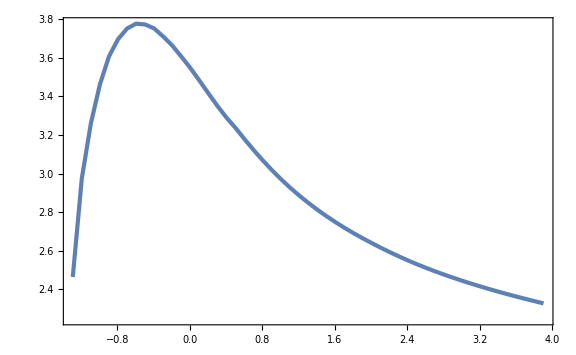

```mathematica
ListPlot[Cbar2List]
```

```mathematica
Cbar2m1List=Table[{mu,Cbar2[mu,-1]//Quiet},{mu,10^-2,1.1,10^-1}];//AbsoluteTiming
```

{0.382744,Null}

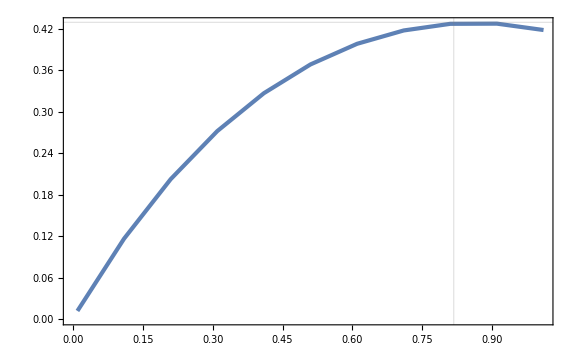

```mathematica
ListPlot[Cbar2m1List,GridLines->{{muthAlbint[-1]},{0.43}}]
```

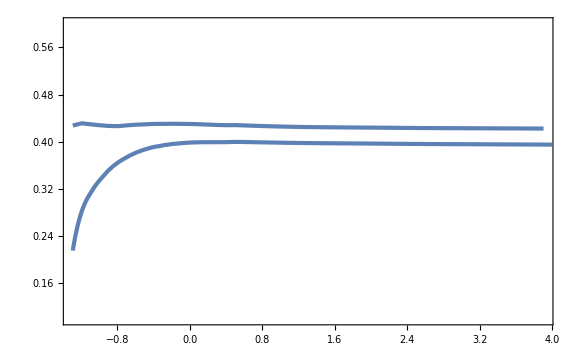

```mathematica
Show[ListPlot[Cbar2List,PlotRange->{0.1,0.6}],Plot[Cbarmint[fNL,muthAlbint[fNL]],{fNL,fNLminAlb,4},PlotRange->Full]]
```

```mathematica
Cb[z_]=Cm z^2 Exp[1/q(1-z^(2q))];
```

```mathematica
zmax=z/.Solve[Cb'[z]==0,z][[2]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

1

```mathematica
Cb[zmax]
```

Cm

```mathematica
-(Cb''[zmax] zmax^2)/(4Cb[zmax])//Simplify
```

q

```mathematica
3/zmax^3 Integrate[Cb[z] z^2,{z,0,zmax}]
```

3/2 Cm ⅇ^(1/q) (1/q)^(1-5/(2 q)) (Gamma[5/(2 q)]-Gamma[5/(2 q),1/q])

```mathematica
Cpp[x_,mu_,fNL_]=D[D[CompactC[x,mu,fNL], x], x]//Simplify
```

1/(75 x^6)4 (-10 (5 x^2+mu (x Cos[x]-Sin[x]) (5 x+6 fNL mu Sin[x]))^2+8 x (5 x^2+mu (x Cos[x]-Sin[x]) (5 x+6 fNL mu Sin[x])) (10 x+mu (5+6 fNL mu Cos[x]) (x Cos[x]-Sin[x])-mu x Sin[x] (5 x+6 fNL mu Sin[x]))-x^2 (10 x+mu (5+6 fNL mu Cos[x]) (x Cos[x]-Sin[x])-mu x Sin[x] (5 x+6 fNL mu Sin[x]))^2+x^2 (5 x^2-5 mu x Sin[x]-6 fNL mu^2 Sin[x]^2+mu x Cos[x] (5 x+6 fNL mu Sin[x])) (mu x Cos[x] (5 x+24 fNL mu Sin[x])+5 (-2+3 mu x Sin[x])))

```mathematica
qq[mu_,fNL_]=-((xmint[mu fNL]^2 Cpp[xmint[mu fNL],mu,fNL])/(4(1-3/2 CompactC[xmint[mu fNL],mu,fNL])CompactC[xmint[mu fNL],mu,fNL]));
```

```mathematica
Clear[Cbarmq]
```

```mathematica
Cbarmq[mu_,fNL_]:=3/2 E^(1/qq[mu,fNL])qq[mu,fNL]^(-1+5/(2qq[mu,fNL]))(Gamma[5/(2qq[mu,fNL])]-Gamma[5/(2qq[mu,fNL]),1/qq[mu,fNL]])CompactC[xmint[mu fNL],mu,fNL]/;mu<mu2int[fNL]
Cbarmq[mu_,fNL_]:=None/;!(mu<mu2int[fNL])
```

```mathematica
FindRoot[Cbarmq[mu,-13/10]==2/5,{mu,1/4}]
```

{mu→0.846324}

```mathematica
FindMaximum[{Cbarmq[mu,-1.3],10^-2≤mu≤mu2int[-1.3]},{mu,1/4}]
```

{0.40191,{mu→0.918181}}

```mathematica
mu2int[-1.3]
```

0.989809

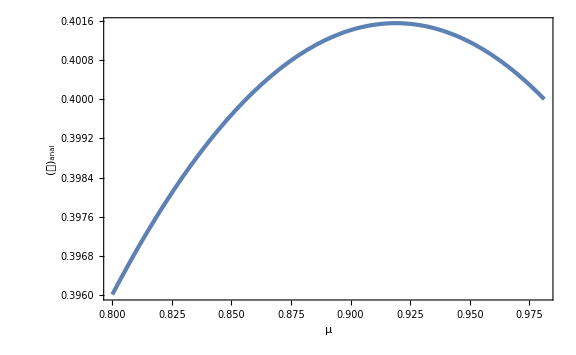

```mathematica
Plot[Cbarmq[mu,-1.5],{mu,0.8,mu2int[-1.5]},GridLines->{None,{2/5}},FrameLabel->{{Subscript[OverBar[𝒞], anal],None},{μ,Subscript[f, NL]==-1.5}}]
```

```mathematica
CbarmqmaxData=ParallelTable[{fNL,FindMaximum[{Cbarmq[mu,fNL],10^-2≤mu≤mu2int[fNL]},{mu,1/4}]},{fNL,-4,4,1/100}];//AbsoluteTiming
```

{133.831,Null}

```mathematica
CbarmqmaxList=Table[{CbarmqmaxData[[i,1]],CbarmqmaxData[[i,2,1]]},{i,Length[CbarmqmaxData]}];
muqmaxList=Table[{CbarmqmaxData[[i,1]],mu/.CbarmqmaxData[[i,2,2]]},{i,Length[CbarmqmaxData]}];
```

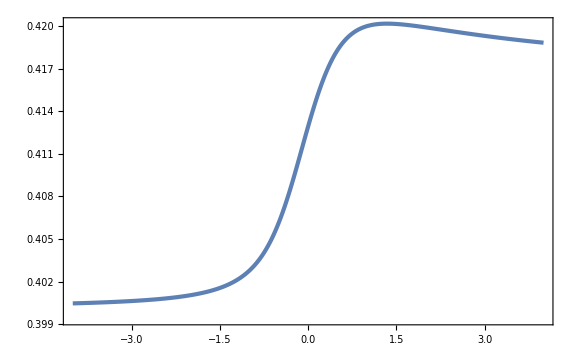

```mathematica
ListPlot[CbarmqmaxList]
```

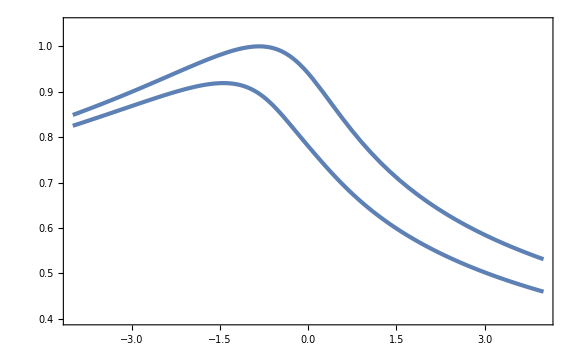

```mathematica
Show[ListPlot[muqmaxList,PlotRange->{0.4,1.05}],Plot[mu2int[fNL],{fNL,-4,4}]]
```

```mathematica
Cbarqmaxint[fNL_]=Interpolation[CbarmqmaxList][fNL];
```

```mathematica
Cbarqth=Cbarqmaxint[-125/100]
```

0.402021

```mathematica
muthqList=Table[{fNL,mu/.FindRoot[Cbarmq[mu,fNL]==2/5,{mu,1/4}]},{fNL,-4,4,1/100}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
muthAlbData=Import["numerical_results2.dat"];
muthAlbList=Sort[Map[{#[[1]],#[[2]]}&,muthAlbData]];
muthAlbErrorList=Sort[Map[{#[[1]],PlusMinus[#[[2]],#[[3]]]}&,muthAlbData]]
```

{{-1.293,0.978001±0.0101111},{-1.2543,0.938721±0.0101111},{-1.2,0.895124±0.0101111},{-1.1,0.850123±0.0101111},{-1.,0.817548±0.00751444},{-0.95,0.805123±0.0051441},{-0.9,0.785348±0.0051441},{-0.85,0.77013±0.005},{-0.8,0.755012±0.0050111},{-0.75,0.745157±0.00202355},{-0.7,0.739453±0.00117187},{-0.65,0.730078±0.00117188},{-0.6,0.718359±0.00117187},{-0.55,0.706641±0.00117188},{-0.5,0.694922±0.00117187},{-0.45,0.685547±0.00117188},{-0.4,0.676172±0.00117187},{-0.35,0.662109±0.00117188},{-0.3,0.655078±0.00117188},{-0.25,0.645703±0.00117187},{-0.2,0.638672±0.00117187},{-0.15,0.629297±0.00117188},{-0.1,0.622266±0.00117188},{-0.05,0.615234±0.00117187},{0.,0.608203±0.00117188},{0.5,0.550655±0.00408789},{1.,0.507195±0.00386418},{1.5,0.474574±0.00161284},{2.,0.44821±0.00241318},{2.5,0.425424±0.00225172},{3.,0.406132±0.00111718},{3.5,0.389322±0.00100362},{4.,0.374397±0.00181457}}

```mathematica
fNLminAlb=muthAlbList[[1,1]]
```

-1.293

```mathematica
muthAlbint[fNL_]=Interpolation[muthAlbList][fNL];
```

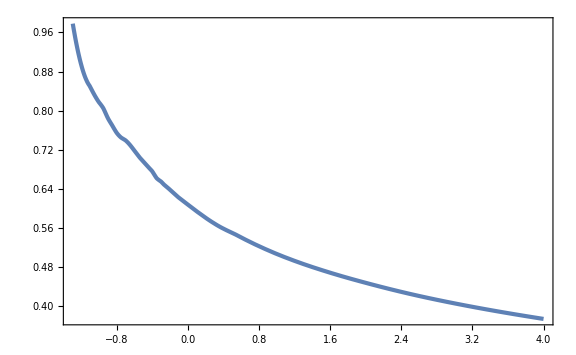

```mathematica
Plot[muthAlbint[fNL],{fNL,fNLminAlb,4}]
```

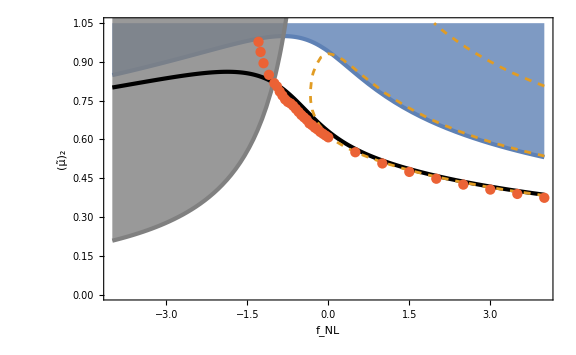

```mathematica
Show[Plot[mu2int[fNL],{fNL,-4,4},Filling->Top,FillingStyle->Opacity[0.8],PlotRange->{0,1.05},FrameLabel->{Subscript[f, NL],Subscript[OverTilde[μ], 2]}],Plot[-5/(6fNL),{fNL,-4,0},PlotStyle->{Gray,AbsoluteThickness[3]},Filling->Top,FillingStyle->Opacity[0.8]],ListPlot[muthqList,PlotStyle->{Black,AbsoluteThickness[3]}],ContourPlot[Cbarmint[fNL,mu]==2/5,{fNL,-4,4},{mu,10^-2,1.05},ContourStyle->{Dashed,Color[2],AbsoluteThickness[2]}],ListPlot[muthAlbErrorList,Joined->False,PlotStyle->Directive[Large,Color[4]]]]
```

```mathematica
Normal[Series[CompactC[x,muthAlbint[0],0],{x,xmint[muthAlbint[0]0],2}]]
```

0.583398+9.4739×10^-17 (-2.74371+x)-0.111868 (-2.74371+x)^2

```mathematica
qtilde[mu_,fNL_]=-(xmint[mu fNL]^2 Cpp[xmint[mu fNL],mu,fNL])/CompactC[xmint[mu fNL],mu,fNL];
```

```mathematica
CmAlbList=Table[{fNL,CompactC[xmint[muthAlbint[fNL]fNL],muthAlbint[fNL],fNL]},{fNL,fNLminAlb,4,1/100}];
qAlbList=Table[{fNL,qtilde[muthAlbint[fNL],fNL]},{fNL,fNLminAlb,4,1/100}];
```

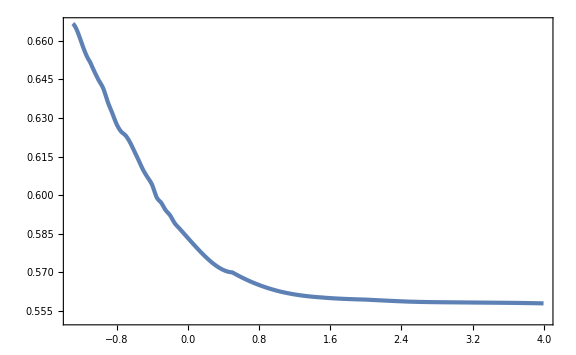

```mathematica
ListPlot[CmAlbList]
```

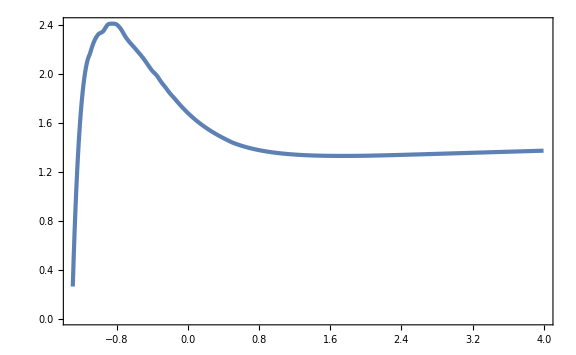

```mathematica
ListPlot[qAlbList]
```

```mathematica
CmAlbint[fNL_]=Interpolation[CmAlbList][fNL];
qAlbint[fNL_]=Interpolation[qAlbList][fNL];
```

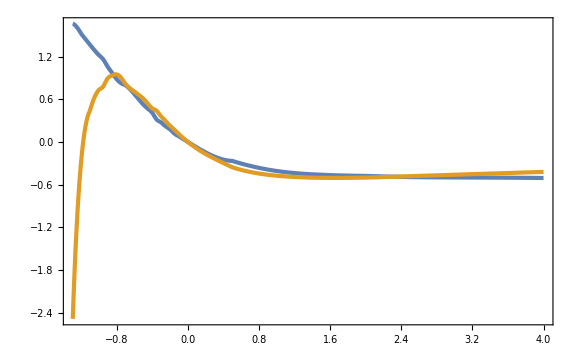

```mathematica
Plot[{20(CmAlbint[fNL]-CmAlbint[0]),qAlbint[fNL]-qAlbint[0]},{fNL,fNLminAlb,4}]
```

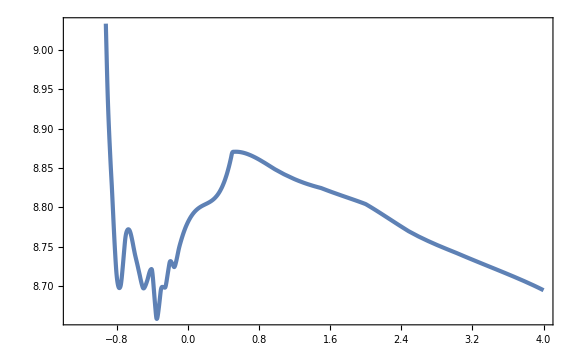

```mathematica
Plot[20CmAlbint[fNL]-qAlbint[fNL],{fNL,fNLminAlb,4}]
```

```mathematica
qAlbint[0]
```

2.88701

```mathematica
muthAlbint[-1]
```

0.817548

```mathematica
CompactC[xmint[muthint[fNLmin]fNLmin],muthint[fNLmin],fNLmin]
CompactC[xmint[muthint[0]0],muthint[0],0]
CompactC[xmint[muthint[4]4],muthint[4],4]
```

0.639184

0.586929

0.568615

InterpolatingFunction::dmval: Input value {-0.335546,0.0000200342} lies outside the range of data in the interpolating function. Extrapolation will be used.

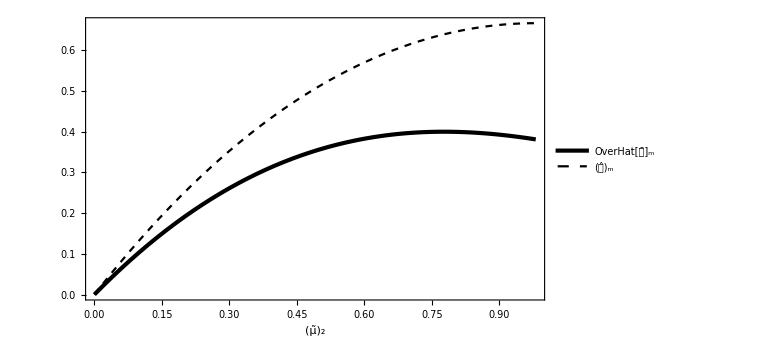

```mathematica
Plot[{Cbarmint[fNLmin,mu],CompactC[xmint[mu fNLmin],mu,fNLmin]},{mu,0,mu2int[fNLmin]},PlotStyle->{{AbsoluteThickness[3],Black},{Dashed,Black}},FrameLabel->{{None,None},{Subscript[OverTilde[μ], 2],Subscript[f, NL]==fNLmin}},PlotLegends->Placed[{Subscript[OverHat[OverBar[𝒞]], "m"],Subscript[OverHat[𝒞], "m"]},{0.9,0.2}],GridLines->{{muthint[fNLmin]},{2/5}}]
```

```mathematica
muthint[fNLmin]
```

0.776553

```mathematica
alpha[mu_,fNL_]=KK(mu-muthint[fNL])^γ/.{KK->1,γ->0.36};
```

```mathematica
MoMks[mu_,fNL_]=xmint[mu fNL]^2 Exp[2zetabar[xmint[mu fNL],mu,fNL]]alpha[mu,fNL];
dLogMdmu[mu_,fNL_]=D[Log[MoMks[mu,fNL]], mu]//Simplify;
```

```mathematica
muthint[4]
```

0.383258

```mathematica
PlotMoMks[mu_,fNL_]:=MoMks[mu,fNL]/;(mu≥muthint[fNL]&&mu≤mu2int[fNL])
PlotMoMks[mu_,fNL_]:=None/;(mu<muthint[fNL]||mu>mu2int[fNL])
```

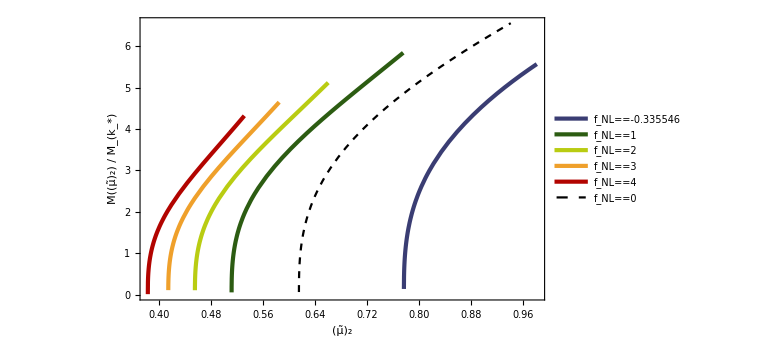

```mathematica
Plot[{PlotMoMks[mu,fNLmin],PlotMoMks[mu,1],PlotMoMks[mu,2],PlotMoMks[mu,3],PlotMoMks[mu,4],PlotMoMks[mu,0]},{mu,muthint[4],mu2int[fNLmin]},FrameLabel->{Subscript[OverTilde[μ], 2],Row[{M[Subscript[OverTilde[μ], 2]]," / ",Subscript[M, Subscript[k, "*"]]}]},PlotStyle->{{AbsoluteThickness[3],ColorData[10,"ColorList"][[9]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[7]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[5]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[3]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[1]]},{Black,Dashed}},PlotLegends->Placed[LineLegend[{Subscript[f, NL]==fNLmin,Subscript[f, NL]==1,Subscript[f, NL]==2,Subscript[f, NL]==3,Subscript[f, NL]==4,Subscript[f, NL]==0},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendLayout->{"Row",2},LegendMarkerSize->20],{0.32,0.87}]]
```

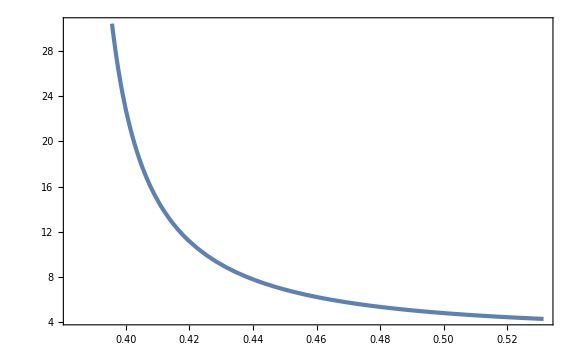

```mathematica
Plot[dLogMdmu[mu,4],{mu,muthint[4],mu2int[4]}]
```

```mathematica
f[z_]=1/2 z(z^2-3)(Erf[1/2 √(5/2)z]+Erf[√(5/2)z])+√(2/(5π))((8/5+31/4 z^2)Exp[-5/8 z^2]+(-8/5+1/2 z^2)Exp[-5/2 z^2]);
```

```mathematica
gineV=(1.783 10^-33)^-1;
MpcinvineV=(10^6 3.086 10^16)^-1 1.973 10^-7;
KineV=(1.16 10^4)^-1;
MplineV=2.435 10^(18+9);
kminvsinvMpcineV=(10^3 6.582 10^-16)/(3.086 10^16 10^6);
keq=0.07 0.143
```

0.01001

```mathematica
((10^20 gineV(3/(2π))^(3/2)(1.56 10^13 MpcinvineV)^3)/(0.12 3 MplineV^2(100 kminvsinvMpcineV)^2))^-1
```

5.28928×10^-16

```mathematica
PG[x_,sg2_]=1/(√(2π sg2))Exp[-x^2/(2sg2)];
```

```mathematica
1/(6.4 10^-14)
```

1.5625×10^13

```mathematica
fPBH[Mks_,ks_,As_,mu_,fNL_]=Mks/10^20 MoMks[mu,fNL](ks/(1.56 10^13))^3(f[mu/(√As)]PG[mu,As])/(5.3 10^-16)Abs[dLogMdmu[mu,fNL]]^-1 UnitStep[mu-muthint[fNL]];
```

```mathematica
fPBH[10^20,1.56 10^13,2 10^-3,muthint[4]+10^-2,4]
```

6.29938

```mathematica
fPBHListfNLmin=Flatten[ParallelTable[{MoMks[muthint[fNLmin]+10^logmu,fNLmin],10^logA,fPBH[10^20,1.56 10^13,10^logA,muthint[fNLmin]+10^logmu,fNLmin]//Quiet},{logmu,-10,Log10[mu2int[fNLmin]-muthint[fNLmin]],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
fPBHListfNL0=Flatten[ParallelTable[{MoMks[muthint[0]+10^logmu,0],10^logA,fPBH[10^20,1.56 10^13,10^logA,muthint[0]+10^logmu,0]//Quiet},{logmu,-10,Log10[mu2int[0]-muthint[0]],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
fPBHListfNL1=Flatten[ParallelTable[{MoMks[muthint[1]+10^logmu,1],10^logA,fPBH[10^20,1.56 10^13,10^logA,muthint[1]+10^logmu,1]//Quiet},{logmu,-10,Log10[mu2int[1]-muthint[1]],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
fPBHListfNL2=Flatten[ParallelTable[{MoMks[muthint[2]+10^logmu,2],10^logA,fPBH[10^20,1.56 10^13,10^logA,muthint[2]+10^logmu,2]//Quiet},{logmu,-10,Log10[mu2int[2]-muthint[2]],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
fPBHListfNL3=Flatten[ParallelTable[{MoMks[muthint[3]+10^logmu,3],10^logA,fPBH[10^20,1.56 10^13,10^logA,muthint[3]+10^logmu,3]//Quiet},{logmu,-10,Log10[mu2int[3]-muthint[3]],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
fPBHListfNL4=Flatten[ParallelTable[{MoMks[muthint[4]+10^logmu,4],10^logA,fPBH[10^20,1.56 10^13,10^logA,muthint[4]+10^logmu,4]//Quiet},{logmu,-10,Log10[mu2int[4]-muthint[4]],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
```

{153.884,Null}

{152.89,Null}

{152.511,Null}

{154.611,Null}

{150.239,Null}

{149.128,Null}

```mathematica
fPBHListfNL52=Flatten[ParallelTable[{MoMks[muthint[5/2]+10^logmu,5/2],10^logA,fPBH[10^20,1.56 10^13,10^logA,muthint[5/2]+10^logmu,5/2]//Quiet},{logmu,-10,Log10[mu2int[5/2]-muthint[5/2]],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
```

{152.35,Null}

```mathematica
Export["fPBHfNLmin.dat",fPBHListfNLmin];
Export["fPBHfNL0.dat",fPBHListfNL0];
Export["fPBHfNL1.dat",fPBHListfNL1];
Export["fPBHfNL2.dat",fPBHListfNL2];
Export["fPBHfNL3.dat",fPBHListfNL3];
Export["fPBHfNL4.dat",fPBHListfNL4];
Export["fPBHfNL52.dat",fPBHListfNL52];
```

```mathematica
fPBHListfNLmin=Import["fPBHfNLmin.dat"]//ToExpression;
fPBHListfNL0=Import["fPBHfNL0.dat"]//ToExpression;
fPBHListfNL1=Import["fPBHfNL1.dat"]//ToExpression;
fPBHListfNL2=Import["fPBHfNL2.dat"]//ToExpression;
fPBHListfNL3=Import["fPBHfNL3.dat"]//ToExpression;
fPBHListfNL4=Import["fPBHfNL4.dat"]//ToExpression;
fPBHListfNL52=Import["fPBHfNL52.dat"]//ToExpression;
```

```mathematica
fPBHintfNLmin[M_,A_]=Interpolation[fPBHListfNLmin][M,A]UnitStep[MoMks[mu2int[fNLmin],fNLmin]-M,M-MoMks[muthint[fNLmin]+10^-10,fNLmin]];
fPBHintfNL0[M_,A_]=Interpolation[fPBHListfNL0][M,A]UnitStep[MoMks[mu2int[0],0]-M,M-MoMks[muthint[0]+10^-10,0]];
fPBHintfNL1[M_,A_]=Interpolation[fPBHListfNL1][M,A]UnitStep[MoMks[mu2int[1],1]-M,M-MoMks[muthint[1]+10^-10,1]];
fPBHintfNL2[M_,A_]=Interpolation[fPBHListfNL2][M,A]UnitStep[MoMks[mu2int[2],2]-M,M-MoMks[muthint[2]+10^-10,2]];
fPBHintfNL3[M_,A_]=Interpolation[fPBHListfNL3][M,A]UnitStep[MoMks[mu2int[3],3]-M,M-MoMks[muthint[3]+10^-10,3]];
fPBHintfNL4[M_,A_]=Interpolation[fPBHListfNL4][M,A]UnitStep[MoMks[mu2int[4],4]-M,M-MoMks[muthint[4]+10^-10,4]];
```

```mathematica
fPBHintfNL52[M_,A_]=Interpolation[fPBHListfNL52][M,A]UnitStep[MoMks[mu2int[5/2],5/2]-M,M-MoMks[muthint[5/2]+10^-10,5/2]];
```

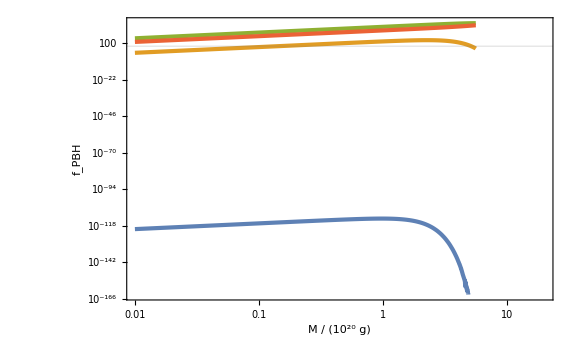

```mathematica
LogLogPlot[{fPBHintfNLmin[M,10^-3],fPBHintfNLmin[M,10^-2],fPBHintfNLmin[M,10^-1],fPBHintfNLmin[M,1]},{M,0.01,20},GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^20 g)"}],Subscript[f, PBH]},PlotRange->Full]
```

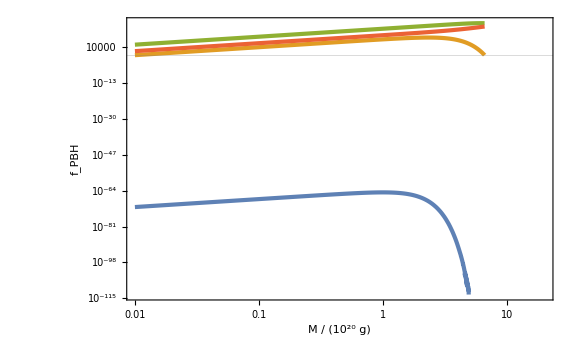

```mathematica
LogLogPlot[{fPBHintfNL0[M,10^-3],fPBHintfNL0[M,10^-2],fPBHintfNL0[M,10^-1],fPBHintfNL0[M,1]},{M,0.01,20},GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^20 g)"}],Subscript[f, PBH]},PlotRange->Full]
```

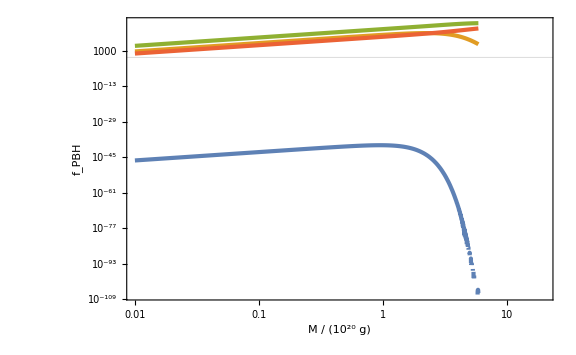

```mathematica
LogLogPlot[{fPBHintfNL1[M,10^-3],fPBHintfNL1[M,10^-2],fPBHintfNL1[M,10^-1],fPBHintfNL1[M,1]},{M,0.01,20},GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^20 g)"}],Subscript[f, PBH]},PlotRange->Full]
```

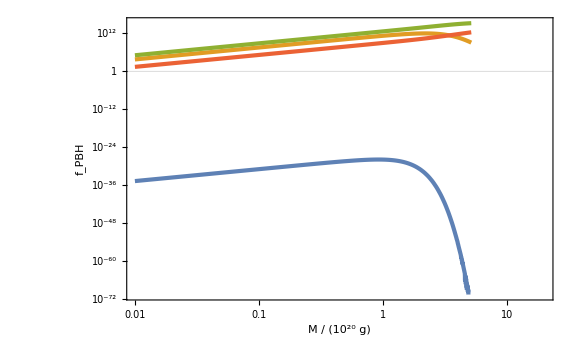

```mathematica
LogLogPlot[{fPBHintfNL2[M,10^-3],fPBHintfNL2[M,10^-2],fPBHintfNL2[M,10^-1],fPBHintfNL2[M,1]},{M,0.01,20},GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^20 g)"}],Subscript[f, PBH]},PlotRange->Full]
```

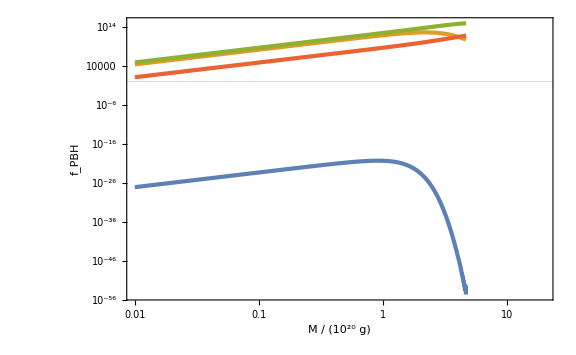

```mathematica
LogLogPlot[{fPBHintfNL3[M,10^-3],fPBHintfNL3[M,10^-2],fPBHintfNL3[M,10^-1],fPBHintfNL3[M,1]},{M,0.01,20},GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^20 g)"}],Subscript[f, PBH]},PlotRange->Full]
```

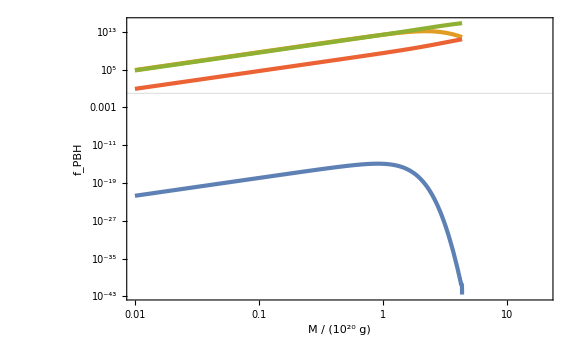

```mathematica
LogLogPlot[{fPBHintfNL4[M,10^-3],fPBHintfNL4[M,10^-2],fPBHintfNL4[M,10^-1],fPBHintfNL4[M,1]},{M,0.01,20},GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^20 g)"}],Subscript[f, PBH]},PlotRange->Full]
```

```mathematica
NIntegrate[fPBHintfNLmin[E^logM,3 10^-3],{logM,Log[10^-2],Log[10]}]
```

2.0659×10^-27

```mathematica
Log10[2 10^-4]//N
```

-3.69897

```mathematica
fPBHAListfNLmin=ParallelTable[{10^logA,NIntegrate[fPBHintfNLmin[E^logM,10^logA],{logM,Log[10^-2],Log[10]}]},{logA,-3,0,10^-2}];//AbsoluteTiming
fPBHAListfNL0=ParallelTable[{10^logA,NIntegrate[fPBHintfNL0[E^logM,10^logA],{logM,Log[10^-2],Log[10]}]},{logA,-3,0,10^-2}];//AbsoluteTiming
fPBHAListfNL1=ParallelTable[{10^logA,NIntegrate[fPBHintfNL1[E^logM,10^logA],{logM,Log[10^-2],Log[10]}]},{logA,-3,0,10^-2}];//AbsoluteTiming
fPBHAListfNL2=ParallelTable[{10^logA,NIntegrate[fPBHintfNL2[E^logM,10^logA],{logM,Log[10^-2],Log[10]}]},{logA,-7/2,0,10^-2}];//AbsoluteTiming
fPBHAListfNL3=ParallelTable[{10^logA,NIntegrate[fPBHintfNL3[E^logM,10^logA],{logM,Log[10^-2],Log[10]}]},{logA,-7/2,0,10^-2}];//AbsoluteTiming
fPBHAListfNL4=ParallelTable[{10^logA,NIntegrate[fPBHintfNL4[E^logM,10^logA],{logM,Log[10^-2],Log[10]}]},{logA,-7/2,0,10^-2}];//AbsoluteTiming
```

{27.2636,Null}

{30.5257,Null}

{29.3713,Null}

{34.2407,Null}

{32.9582,Null}

{32.8636,Null}

```mathematica
fPBHAListfNL52=ParallelTable[{10^logA,NIntegrate[fPBHintfNL52[E^logM,10^logA],{logM,Log[10^-2],Log[10]}]//Quiet},{logA,-7/2,0,10^-2}];//AbsoluteTiming
```

{33.8633,Null}

```mathematica
Export["fPBHAfNLmin.dat",fPBHAListfNLmin];
Export["fPBHAfNL0.dat",fPBHAListfNL0];
Export["fPBHAfNL1.dat",fPBHAListfNL1];
Export["fPBHAfNL2.dat",fPBHAListfNL2];
Export["fPBHAfNL3.dat",fPBHAListfNL3];
Export["fPBHAfNL4.dat",fPBHAListfNL4];
Export["fPBHAfNL52.dat",fPBHAListfNL52];
```

```mathematica
fPBHAListfNLmin=Import["fPBHAfNLmin.dat"]//ToExpression;
fPBHAListfNL0=Import["fPBHAfNL0.dat"]//ToExpression;
fPBHAListfNL1=Import["fPBHAfNL1.dat"]//ToExpression;
fPBHAListfNL2=Import["fPBHAfNL2.dat"]//ToExpression;
fPBHAListfNL3=Import["fPBHAfNL3.dat"]//ToExpression;
fPBHAListfNL4=Import["fPBHAfNL4.dat"]//ToExpression;
fPBHAListfNL52=Import["fPBHAfNL52.dat"]//ToExpression;
```

```mathematica
ColorData[10,"ColorList"]
```

{RGBColor[0.6980392156862745, 0.01568627450980392, 0.],RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786],RGBColor[0.9372549019607843, 0.6274509803921569, 0.16862745098039217],RGBColor[0.9921568627450981, 0.8156862745098039, 0.49019607843137253],RGBColor[0.7254901960784313, 0.8, 0.07058823529411765],RGBColor[0.3176470588235294, 0.49019607843137253, 0.0784313725490196],RGBColor[0.17254901960784313, 0.3607843137254902, 0.07058823529411765],RGBColor[0.3607843137254902, 0.40784313725490196, 0.5333333333333333],RGBColor[0.22745098039215686, 0.23921568627450981, 0.45098039215686275],RGBColor[0.09803921568627451, 0.06666666666666667, 0.25098039215686274],RGBColor[0.5607843137254902, 0.5254901960784314, 0.5647058823529412]}

```mathematica
fNLmin
```

-0.335546

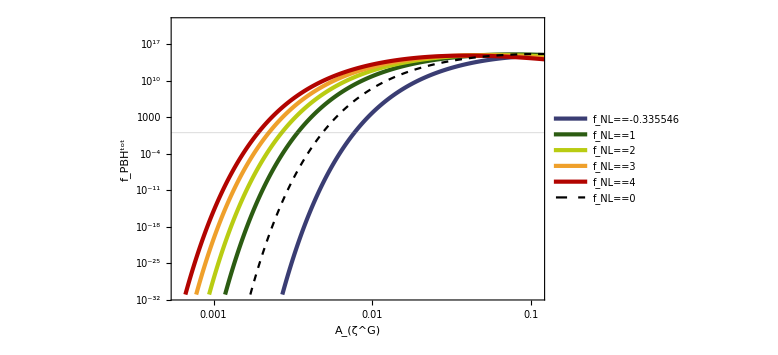

```mathematica
ListLogLogPlot[{fPBHAListfNLmin,fPBHAListfNL1,fPBHAListfNL2,fPBHAListfNL3,fPBHAListfNL4,fPBHAListfNL0},FrameLabel->{Subscript[A, ζ^("G")],Subscript[f, PBH]^tot},PlotRange->{{6 10^-4,1.1 10^-1},{10^-31,10^21}},GridLines->{None,{1}},PlotStyle->{{AbsoluteThickness[3],ColorData[10,"ColorList"][[9]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[7]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[5]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[3]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[1]]},{Black,Dashed}},PlotLegends->Placed[LineLegend[{Subscript[f, NL]==fNLmin,Subscript[f, NL]==1,Subscript[f, NL]==2,Subscript[f, NL]==3,Subscript[f, NL]==4,Subscript[f, NL]==0},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendLayout->{"Column",2},LegendMarkerSize->20],{0.7,0.2}]]
```

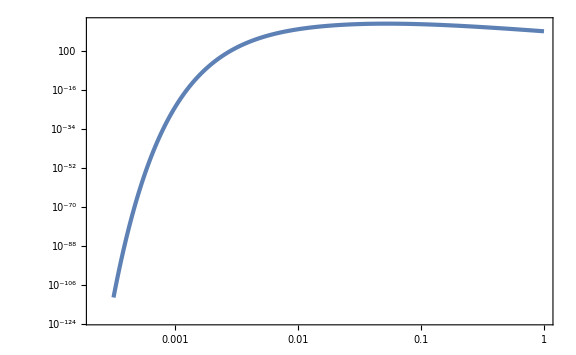

```mathematica
ListLogLogPlot[fPBHAListfNL52]
```

```mathematica
Export["fPBHA_fNL52.dat",fPBHAListfNL52];
```

```mathematica
fPBHAListfNL52=Import["fPBHA_fNL52.dat"]//ToExpression;
```

```mathematica
ListLogLogPlot[fPBHAListfNL52]
```

-Graphics-

```mathematica
fPBHAintfNLmin[A_]=Interpolation[fPBHAListfNLmin][A];
fPBHAintfNL0[A_]=Interpolation[fPBHAListfNL0][A];
fPBHAintfNL1[A_]=Interpolation[fPBHAListfNL1][A];
fPBHAintfNL2[A_]=Interpolation[fPBHAListfNL2][A];
fPBHAintfNL3[A_]=Interpolation[fPBHAListfNL3][A];
fPBHAintfNL4[A_]=Interpolation[fPBHAListfNL4][A];
```

```mathematica
fPBHAintfNL52[A_]=Interpolation[fPBHAListfNL52][A];
```

```mathematica
A1fNLmin=A/.FindRoot[Log10[fPBHAintfNLmin[A]]==0,{A,0.005}]
A1fNL0=A/.FindRoot[Log10[fPBHAintfNL0[A]]==0,{A,0.005}]
A1fNL1=A/.FindRoot[Log10[fPBHAintfNL1[A]]==0,{A,0.003}]
A1fNL2=A/.FindRoot[Log10[fPBHAintfNL2[A]]==0,{A,0.003}]
A1fNL3=A/.FindRoot[Log10[fPBHAintfNL3[A]]==0,{A,0.003}]
A1fNL4=A/.FindRoot[Log10[fPBHAintfNL4[A]]==0,{A,0.003}]
```

0.00771511

0.00486276

0.00338132

0.00268592

0.00222991

0.00190794

```mathematica
A1fNL52=A/.FindRoot[Log10[fPBHAintfNL52[A]]==0,{A,0.003}]
```

0.00243682

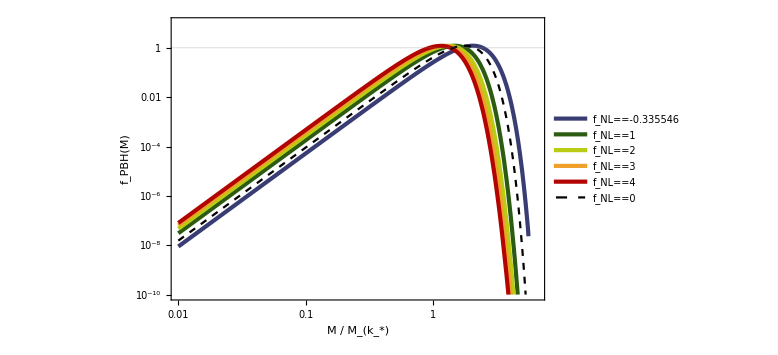

```mathematica
LogLogPlot[{fPBHintfNLmin[M,A1fNLmin],fPBHintfNL1[M,A1fNL1],fPBHintfNL2[M,A1fNL2],fPBHintfNL3[M,A1fNL3],fPBHintfNL4[M,A1fNL4],fPBHintfNL0[M,A1fNL0]},{M,0.01,10},GridLines->{None,{1}},FrameLabel->{Row[{M," / ",Subscript[M, SubStar[k]]}],Subscript[f, PBH][M]},PlotRange->{10^-10,10},PlotStyle->{{AbsoluteThickness[3],ColorData[10,"ColorList"][[9]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[7]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[5]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[3]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[1]]},{Black,Dashed}},PlotLegends->Placed[LineLegend[{Subscript[f, NL]==fNLmin,Subscript[f, NL]==1,Subscript[f, NL]==2,Subscript[f, NL]==3,Subscript[f, NL]==4,Subscript[f, NL]==0},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendLayout->{"Column",2},LegendMarkerSize->20],{0.6,0.2}]]
```

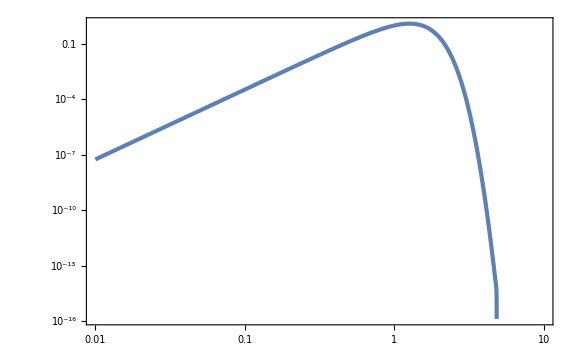

```mathematica
LogLogPlot[fPBHintfNL52[M,A1fNL52],{M,0.01,10}]
```

```mathematica
Export["fPBHint_fNL52.wdx",fPBHintfNL52[M,A1fNL52]];
```

```mathematica
fPBHA1fNL52[M_]=Import["fPBHint_fNL52.wdx"];
```

```mathematica
LogLogPlot[fPBHA1fNL52[M],{M,0.01,10}]
```

-Graphics-

#### Press-Schechter

```mathematica
xm=2.74;
```

```mathematica
WRTH[z_]=3/z^3(Sin[z]-z Cos[z]);
```

```mathematica
sX[A_]=4/9 xm^2 WRTH[xm]Sqrt[A]
sY[A_,fNL_]=6/4 fNL Sinc[xm]Sqrt[A]
```

1.41746 √A

0.213988 √A fNL

```mathematica
PfNL[dl_,A_,fNL_]=1/Sqrt[2π sX[A]^2](Exp[(-((-sX[A]+Sqrt[sX[A]^2+4sX[A]sY[A,fNL]dl])/(2sY[A,fNL]))^2)/(2 sX[A]^2)]+Exp[(-((-sX[A]-Sqrt[sX[A]^2+4sX[A]sY[A,fNL]dl])/(2sY[A,fNL]))^2)/(2 sX[A]^2)])//Simplify
PGauss[dl_,A_]=1/Sqrt[2π sX[A]^2] Exp[Normal[Series[-((-sX[A]+Sqrt[sX[A]^2+4sX[A]sY[A,fNL]dl])/(2sY[A,fNL]))^2,{fNL,0,0}]]/(2 sX[A]^2)]//Simplify
```

1/(√A)0.281448 (ⅇ^(-(1.35865 (-1.41746 √A+√(A (2.00921+1.21328 dl fNL)))^2)/(A^2 fNL^2))+ⅇ^(-(1.35865 (1.41746 √A+√(A (2.00921+1.21328 dl fNL)))^2)/(A^2 fNL^2)))

(0.281448 ⅇ^(-(0.248855 dl^2)/A))/(√A)

General::munfl: Exp[-10658.] is too small to represent as a normalized machine number; precision may be lost.

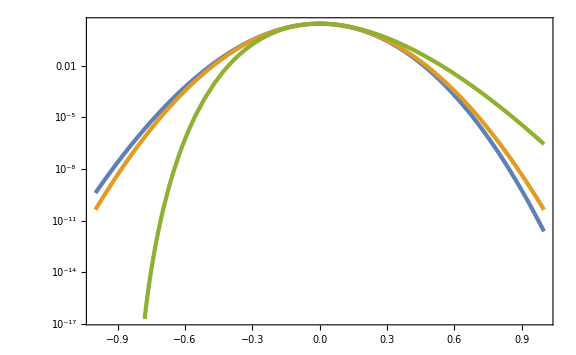

```mathematica
LogPlot[{PfNL[dl,10^-2,fNLmin],PGauss[dl,10^-2],PfNL[dl,10^-2,2]},{dl,-1,1}]
```

```mathematica
MoMksPS[dl_]=xm^2 KK(dl-3/8 dl^2-Cth)^γ/.{KK->1,γ->0.36,Cth->0.587}
β[dl_,A_,fNL_]=(KK(dl-3/8 dl^2-Cth)^(γ+1))/(γ(1-3/4 dl))PfNL[dl,A,fNL]/.{KK->1,γ->0.36,Cth->0.587}

βGauss[dl_,A_]=(KK(dl-3/8 dl^2-Cth)^(γ+1))/(γ(1-3/4 dl))PGauss[dl,A]/.{KK->1,γ->0.36,Cth->0.587}
fPBHPS[dl_,A_,fNL_]=β[dl,A,fNL]/(6.88 10^-16);
fPBHPSGauss[dl_,A_]=βGauss[dl,A]/(6.88 10^-16);
```

7.5076 (-0.587+dl-(3 dl^2)/8)^0.36

1/(√A (1-(3 dl)/4))0.7818 (-0.587+dl-(3 dl^2)/8)^1.36 (ⅇ^(-(1.35865 (-1.41746 √A+√(A (2.00921+1.21328 dl fNL)))^2)/(A^2 fNL^2))+ⅇ^(-(1.35865 (1.41746 √A+√(A (2.00921+1.21328 dl fNL)))^2)/(A^2 fNL^2)))

(0.7818 (-0.587+dl-(3 dl^2)/8)^1.36 ⅇ^(-(0.248855 dl^2)/A))/(√A (1-(3 dl)/4))

```mathematica
dlth=4/3(1-Sqrt[1-3/2 Cth])/.{Cth->0.587}
dlmax=4/3;
```

0.872416

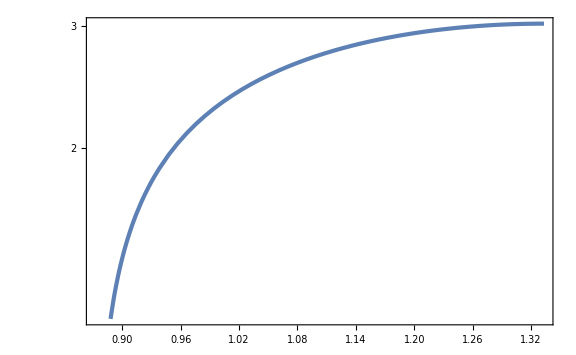

```mathematica
LogPlot[MoMksPS[dl],{dl,dlth,dlmax}]
```

```mathematica
fPBHPSListfNLmin=Flatten[ParallelTable[{MoMksPS[dlth+10^logdl],10^logA,fPBHPS[dlth+10^logdl,10^logA,fNLmin]//Quiet},{logdl,-10,Log10[dlmax-dlth],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
fPBHPSListfNL0=Flatten[ParallelTable[{MoMksPS[dlth+10^logdl],10^logA,fPBHPSGauss[dlth+10^logdl,10^logA]//Quiet},{logdl,-10,Log10[dlmax-dlth],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
fPBHPSListfNL2=Flatten[ParallelTable[{MoMksPS[dlth+10^logdl],10^logA,fPBHPS[dlth+10^logdl,10^logA,2]//Quiet},{logdl,-10,Log10[dlmax-dlth],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
fPBHPSListfNL4=Flatten[ParallelTable[{MoMksPS[dlth+10^logdl],10^logA,fPBHPS[dlth+10^logdl,10^logA,4]//Quiet},{logdl,-10,Log10[dlmax-dlth],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
```

{7.4048,Null}

{4.99572,Null}

{7.26934,Null}

{6.84714,Null}

```mathematica
Export["fPBHPSfNLmin.dat",fPBHPSListfNLmin];
Export["fPBHPSfNL0.dat",fPBHPSListfNL0];
Export["fPBHPSfNL2.dat",fPBHPSListfNL2];
Export["fPBHPSfNL4.dat",fPBHPSListfNL4];
```

```mathematica
fPBHPSListfNLmin=Import["fPBHPSfNLmin.dat"]//ToExpression;
fPBHPSListfNL0=Import["fPBHPSfNL0.dat"]//ToExpression;
fPBHPSListfNL2=Import["fPBHPSfNL2.dat"]//ToExpression;
fPBHPSListfNL4=Import["fPBHPSfNL4.dat"]//ToExpression;
```

```mathematica
Mmax=MoMksPS[dlmax]
Mmin=MoMksPS[dlth+10^-10]
```

3.01968

0.00128655

```mathematica
fPBHPSintfNLmin[M_,A_]=Interpolation[fPBHPSListfNLmin][M,A]UnitStep[Mmax-M,M-Mmin];
fPBHPSintfNL0[M_,A_]=Interpolation[fPBHPSListfNL0][M,A]UnitStep[Mmax-M,M-Mmin];
fPBHPSintfNL2[M_,A_]=Interpolation[fPBHPSListfNL2][M,A]UnitStep[Mmax-M,M-Mmin];
fPBHPSintfNL4[M_,A_]=Interpolation[fPBHPSListfNL4][M,A]UnitStep[Mmax-M,M-Mmin];
```

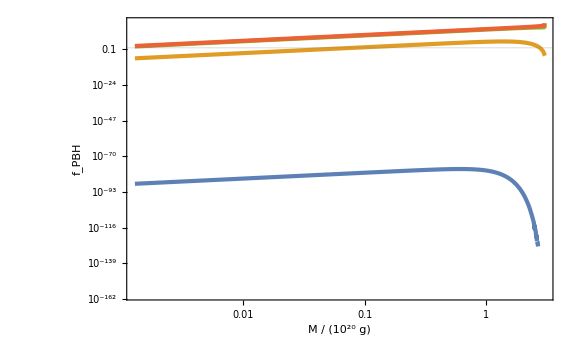

```mathematica
LogLogPlot[{fPBHPSintfNLmin[M,10^-3],fPBHPSintfNLmin[M,10^-2],fPBHPSintfNLmin[M,10^-1],fPBHPSintfNLmin[M,1]},{M,Mmin,Mmax},GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^20 g)"}],Subscript[f, PBH]},PlotRange->Full]
```

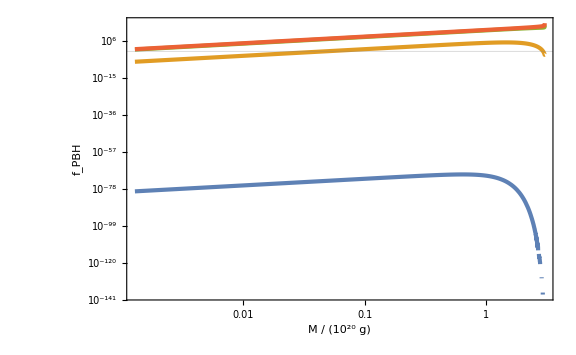

```mathematica
LogLogPlot[{fPBHPSintfNL0[M,10^-3],fPBHPSintfNL0[M,10^-2],fPBHPSintfNL0[M,10^-1],fPBHPSintfNL0[M,1]},{M,Mmin,Mmax},GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^20 g)"}],Subscript[f, PBH]},PlotRange->Full]
```

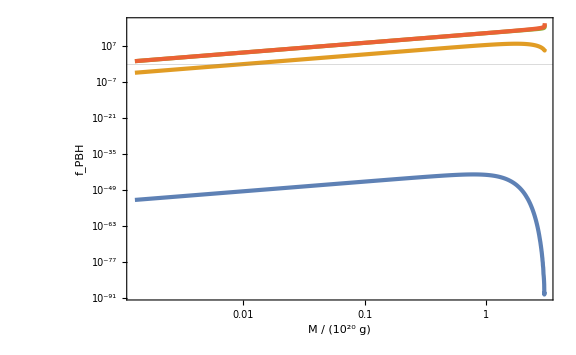

```mathematica
LogLogPlot[{fPBHPSintfNL2[M,10^-3],fPBHPSintfNL2[M,10^-2],fPBHPSintfNL2[M,10^-1],fPBHPSintfNL2[M,1]},{M,Mmin,Mmax},GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^20 g)"}],Subscript[f, PBH]},PlotRange->Full]
```

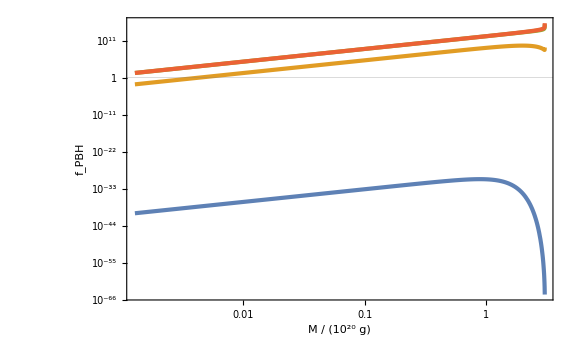

```mathematica
LogLogPlot[{fPBHPSintfNL4[M,10^-3],fPBHPSintfNL4[M,10^-2],fPBHPSintfNL4[M,10^-1],fPBHPSintfNL4[M,1]},{M,Mmin,Mmax},GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^20 g)"}],Subscript[f, PBH]},PlotRange->Full]
```

```mathematica
fPBHAPSListfNLmin=ParallelTable[{10^logA,NIntegrate[fPBHPSintfNLmin[E^logM,10^logA],{logM,Log[Mmin],Log[Mmax]}]//Quiet},{logA,-4,0,10^-2}];//AbsoluteTiming
fPBHAPSListfNL0=ParallelTable[{10^logA,NIntegrate[fPBHPSintfNL0[E^logM,10^logA],{logM,Log[Mmin],Log[Mmax]}]//Quiet},{logA,-4,0,10^-2}];//AbsoluteTiming
fPBHAPSListfNL2=ParallelTable[{10^logA,NIntegrate[fPBHPSintfNL2[E^logM,10^logA],{logM,Log[Mmin],Log[Mmax]}]//Quiet},{logA,-4,0,10^-2}];//AbsoluteTiming
fPBHAPSListfNL4=ParallelTable[{10^logA,NIntegrate[fPBHPSintfNL4[E^logM,10^logA],{logM,Log[Mmin],Log[Mmax]}]//Quiet},{logA,-4,0,10^-2}];//AbsoluteTiming
```

{9.9394,Null}

{9.95662,Null}

{9.94781,Null}

{10.1006,Null}

```mathematica
Export["fPBHAPSfNLmin.dat",fPBHAPSListfNLmin];
Export["fPBHAPSfNL0.dat",fPBHAPSListfNL0];
Export["fPBHAPSfNL2.dat",fPBHAPSListfNL2];
Export["fPBHAPSfNL4.dat",fPBHAPSListfNL4];
```

```mathematica
fPBHAPSListfNLmin=Import["fPBHAPSfNLmin.dat"]//ToExpression;
fPBHAPSListfNL0=Import["fPBHAPSfNL0.dat"]//ToExpression;
fPBHAPSListfNL2=Import["fPBHAPSfNL2.dat"]//ToExpression;
fPBHAPSListfNL4=Import["fPBHAPSfNL4.dat"]//ToExpression;
```

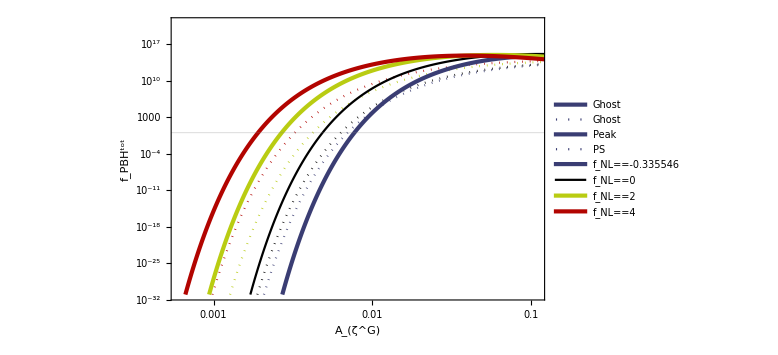

```mathematica
Show[ListLogLogPlot[{fPBHAPSListfNLmin,fPBHAPSListfNL0,fPBHAPSListfNL2,fPBHAPSListfNL4,fPBHAListfNLmin,fPBHAListfNL0,fPBHAListfNL2,fPBHAListfNL4},FrameLabel->{Subscript[A, ζ^("G")],Subscript[f, PBH]^tot},PlotRange->{{6 10^-4,1.1 10^-1},{10^-31,10^21}},GridLines->{None,{1}},PlotStyle->{{ColorData[10,"ColorList"][[9]],Dotted},{Black,Dotted},{ColorData[10,"ColorList"][[5]],Dotted},{ColorData[10,"ColorList"][[1]],Dotted},{AbsoluteThickness[3],ColorData[10,"ColorList"][[9]]},{Black},{AbsoluteThickness[3],ColorData[10,"ColorList"][[5]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[1]]}}],
LogLogPlot[{0,0,0,0,0,0,0,0},{x,0.1,1},PlotStyle->{{AbsoluteThickness[3],ColorData[10,"ColorList"][[9]]},{Dotted,ColorData[10,"ColorList"][[9]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[9]]},{Dotted,ColorData[10,"ColorList"][[9]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[9]]},{Black},{AbsoluteThickness[3],ColorData[10,"ColorList"][[5]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[1]]}},PlotLegends->Placed[LineLegend[{"Ghost","Ghost","Peak","PS",Subscript[f, NL]==fNLmin,Subscript[f, NL]==0,Subscript[f, NL]==2,Subscript[f, NL]==4},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendMarkerSize->20,LegendLayout->{"Column",2}],{0.75,0.25}]]]
```

```mathematica
fPBHAPSintfNLmin[A_]=Interpolation[fPBHAPSListfNLmin][A];
fPBHAPSintfNL0[A_]=Interpolation[fPBHAPSListfNL0][A];
fPBHAPSintfNL2[A_]=Interpolation[fPBHAPSListfNL2][A];
fPBHAPSintfNL4[A_]=Interpolation[fPBHAPSListfNL4][A];
```

```mathematica
A1PSfNLmin=A/.FindRoot[Log10[fPBHAPSintfNLmin[A]]==0,{A,0.003}]
A1PSfNL0=A/.FindRoot[Log10[fPBHAPSintfNL0[A]]==0,{A,0.003}]
A1PSfNL2=A/.FindRoot[Log10[fPBHAPSintfNL2[A]]==0,{A,0.003}]
A1PSfNL4=A/.FindRoot[Log10[fPBHAPSintfNL4[A]]==0,{A,0.003}]
```

0.00699411

0.00633633

0.00422324

0.00325043

InterpolatingFunction::dmval: Input value {0.000100024,0.00699411} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.000126515,0.00699411} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.000160024,0.00699411} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

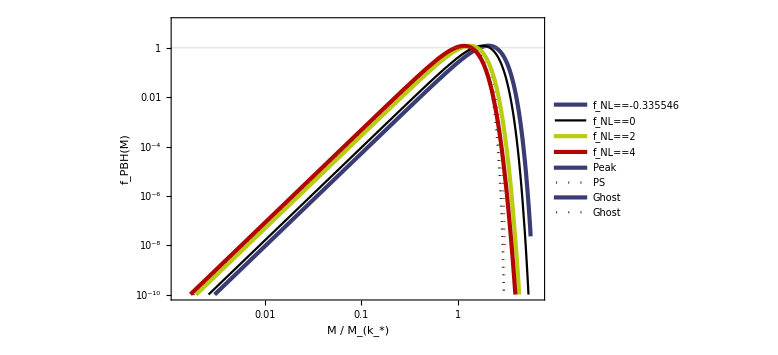

```mathematica
Show[LogLogPlot[{fPBHPSintfNLmin[M,A1PSfNLmin],fPBHPSintfNL0[M,A1PSfNL0],fPBHPSintfNL2[M,A1PSfNL2],fPBHPSintfNL4[M,A1PSfNL4],fPBHintfNLmin[M,A1fNLmin],fPBHintfNL0[M,A1fNL0],fPBHintfNL2[M,A1fNL2],fPBHintfNL4[M,A1fNL4]},{M,10^-4,10},GridLines->{None,{1}},FrameLabel->{Row[{M," / ",Subscript[M, SubStar[k]]}],Subscript[f, PBH][M]},PlotRange->{10^-10,10},PlotStyle->{{ColorData[10,"ColorList"][[9]],Dotted},{Black,Dotted},{ColorData[10,"ColorList"][[5]],Dotted},{ColorData[10,"ColorList"][[1]],Dotted},{AbsoluteThickness[3],ColorData[10,"ColorList"][[9]]},{Black},{AbsoluteThickness[3],ColorData[10,"ColorList"][[5]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[1]]}}],
LogLogPlot[{0,0,0,0,0,0,0,0},{x,0.1,1},PlotStyle->{{AbsoluteThickness[3],ColorData[10,"ColorList"][[9]]},{Black},{AbsoluteThickness[3],ColorData[10,"ColorList"][[5]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[1]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[9]]},{Dotted,ColorData[10,"ColorList"][[9]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[9]]},{Dotted,ColorData[10,"ColorList"][[9]]}},PlotLegends->Placed[LineLegend[{Subscript[f, NL]==fNLmin,Subscript[f, NL]==0,Subscript[f, NL]==2,Subscript[f, NL]==4,"Peak","PS","Ghost","Ghost"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendMarkerSize->20,LegendLayout->{"Column",2}],{0.3,0.65}]]]
```